# The Sandpile Model

Jonas Kaufman & Jon Ueki

## Introduction

(intro goes here)

## Graphics Setup

```mathematica
Module[{cmds= {"Plot", "ListPlot", "ListLinePlot", "ListLogPlot", "ListLogLogPlot","LogPlot","LogLogPlot","ListStepPlot"}},
For[j=1, j≤ Length[cmds],j++,SetOptions[Symbol[ cmds[[j]] ], Frame->True,LabelStyle->{Larger, FontFamily->"Utopia"}]]
]
```

## 1-D Model

```mathematica
length=20;
zCrit=1;
```

```mathematica
randomRow[]:=row=Table[RandomInteger[zCrit],{length}]
constantRow[c_]:=row=Table[c,{length}]
```

```mathematica
addGrain[] :=Module[{r},
r=RandomInteger[{1,length}];
row[[r]]++;
If[r>1,row[[r-1]]--]
];
```

```mathematica
relaxation1D[]:=Module[{i,stable=False},
While[!stable,
stable=True;
For[i=1,i≤ length,i++,
If[row[[i]]> zCrit,
stable=False;
If[1<i<length,row[[i]]-=2;row[[i+1]]++;row[[i-1]]++;];
If[i==1,row[[i]]-=2;row[[i+1]]++;];
If[i==length,row[[i]]--;row[[i-1]]++];
];
];
];
]
```

```mathematica
pourSand[numGrains_]:=Module[{n,rows={}},
For[n=1,n≤numGrains,n++,
addGrain[];
relaxation1D[];
AppendTo[rows,row]; 
];
rows
]
```

```mathematica
constantRow[0];
rows=pourSand[1000];
Animate[GraphicsColumn[{
ListStepPlot[Table[Total[rows[[t]][[i;;]]],{i,length}],FrameLabel->{"i","h"},PlotRange->{0,length*zCrit+1}],
ListStepPlot[rows[[t]],FrameLabel->{"i","z"},PlotRange->{-zCrit-1,zCrit+1}]
}],{t,1,Length[rows],1,Appearance->"Labeled"},AnimationRunning->False,AnimationRate->Automatic]
```

## 2-D Model

#### Initialization

```mathematica
Clear["Global`*"]
```

```mathematica
gridsize = 41;
sandRate = 1; (*How many steps to wait before adding more sand *)
zCrit = 4;
addSand[place_, random_] :=Module[{i, x, y}, (*add sand to the middle of the pile *)
If[random==True,(*If we activate random, then add grains randomly*)
addGrainRandom[],

For[i=1, i≤ Length[place], i++,
x=place[[i,1]];
y=place[[i,2]];
grid[[x,y]] += 1;
];
];
]
```

```mathematica
addGrainRandom[]:=Module[{a,b},
{a,b}=RandomInteger[{1,gridsize},2];
grid[[a,b]]++;
];
```

#### Reset Button

```mathematica
reset[]:=grid = Table[Table[0, {n, gridsize}], {n, gridsize}];
```

```mathematica
reset[];
```

```mathematica
heights[grid_]:=Module[{i,j,heights=grid},
For[i=gridsize-1,i>0,i--,
For[j=gridsize-1,j>0,j--,
heights[[i,j]]=0.5(grid[[i,j]]+heights[[i+1,j]]+heights[[i,j+1]]);
];
];
heights
]
```

#### Active Code

Relaxation is repeated until the configuration is stable. s is the total number of topplings and T is the number of relaxation steps.

```mathematica
relaxation[] := Module[{i ,j,s=0,T=0,stable=False},
While [!stable,
stable=True;
For[i=1, i≤ gridsize, i++,
For[j=1, j≤ gridsize, j++,
If[grid[[i,j]] > zCrit,
stable=False;
s++;
grid[[i,j]] -= 4; (*Lose 4 sand*)
(*give sand to the neighbors | Open Boundry Conditions *)
If[i≠ gridsize, grid[[i+1, j]]++];
If[j≠ gridsize, grid[[i, j+1]]++];
If[i≠ 1, grid[[i-1, j]]++];
If[j≠ 1, grid[[i, j-1]]++];
];
];
]; (*end of double for loop *)
If[!stable,T++];
];
{s,T}
]
```

```mathematica
pourSand[totalSand_, random_:False,place_:{{IntegerPart[gridsize/2], IntegerPart[gridsize/2]}}] := Module[{n,s,T,sList={},TList={},grids={}},
For[n=1,n≤ totalSand,n++,
addSand[place, random];
{s,T}=relaxation[];
AppendTo[grids,grid]AppendTo[sList,s];AppendTo[TList,T];
];
{grids,sList,TList}
]
```

#### Gather Statistics

Distribution of slopes

```mathematica
slopeDist[]:= Module[{slopes, slopedist = {}, i, j},
slopes = Table[0, {n, 0, zCrit}];
For[i=1, i≤ gridsize, i++,
For[j=1, j≤gridsize,j++,
slopes[[grid[[i,j]] + 1]]++;
];
];
(*make x-coordinate and y-coordinate pair *)
For[i=1, i≤Length[slopes], i++,
AppendTo[slopedist, {i-1, slopes[[i]]}];
];
slopedist
]
```

#### Run and Plot the Simulation

```mathematica
reset[];
```

```mathematica
{grids,sList,TList}=pourSand[1000, True]; (*Set 3 parameter to true if you want grains to be added in random positions*)
```

```mathematica
Animate[ArrayPlot[grids[[t]]],{t,1,Length[grids],1,Appearance->"Labeled"}]
```

```mathematica
Animate[ArrayPlot[heights[grids[[t]]]],{t,1,Length[grids],1,Appearance->"Labeled"}]
```

```mathematica
(*Dynamic[ArrayPlot[grid,PlotLegends->Automatic]]*)
```

```mathematica
(*Dynamic[ListPlot3D[heights[],InterpolationOrder->0,ColorFunction->"SouthwestColors"]]*)
```

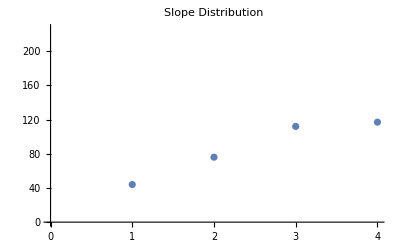

```mathematica
ListPlot[slopeDist[], PlotLabel->"Slope Distribution"]
```